```mathematica
SetDirectory["/Users/brucesawhill/Desktop"]
```

/Users/brucesawhill/Desktop

```mathematica
FileNames[];
```

```mathematica
data=Import["jfkdatatry.csv"];
```

```mathematica
Length[data]
```

167

```mathematica
datatable=Table[Table[data[[i,1]],{i,j,j+4}],{j,8,167,5}]
```

{{14,ARRIVAL_NODE,-1157.5,-442.124,0},{475,TAXI_NODE,-1175.7,-386.941,0},{476,TAXI_NODE,-1172.92,-334.997,0},{124,TAXI_NODE,-1170.65,-291.551,0},{123,TAXI_NODE,-1028.87,-378,0},{122,TAXI_NODE,-854.941,-481.753,0},{121,TAXI_NODE,-707.108,-570.501,0},{120,TAXI_NODE,-402.18,-751.877,0},{119,TAXI_NODE,-72.555,-948.105,0},{118,TAXI_NODE,38.6864,-1011.2,0},{117,TAXI_NODE,134.951,-1025.59,0},{116,TAXI_NODE,206.142,-1006.4,0},{115,TAXI_NODE,287.293,-941.578,0},{114,TAXI_NODE,447.735,-675.038,0},{113,TAXI_NODE,571.681,-470.455,0},{112,TAXI_NODE,687.345,-273.011,0},{111,TAXI_NODE,829.48,-37.6573,0},{110,TAXI_NODE,952.92,182.327,0},{109,TAXI_NODE,964.727,224.036,0},{108,TAXI_NODE,968.045,358.282,0},{107,TAXI_NODE,968.408,420.132,0},{106,TAXI_NODE,923.231,538.91,0},{105,TAXI_NODE,842.939,599.988,0},{104,TAXI_NODE,711.212,678.598,0},{57,TAXI_NODE,666.986,604.075,0},{186,SPOT_NODE,638.581,557.771,0},{625,RAMP_NODE,626.587,532.29,0},{624,RAMP_NODE,665.2,509.757,0},{623,RAMP_NODE,705.011,485.111,0},{622,RAMP_NODE,734.87,465.878,0},{621,RAMP_NODE,794.579,429.221,0},{321,GATE_NODE,789.707,397.692,0}}

```mathematica
Dimensions[datatable]
```

{32,5}

```mathematica
spotnode=ListPlot[{{638.5806,557.7712}},PlotStyle->{Blue,PointSize[.020]}];
arrivalnode=ListPlot[{{-1157.5,-442.124}},PlotStyle->{Green,PointSize[.020]}];
gatenode=ListPlot[{{789.7073,397.692}},PlotStyle->{Red,PointSize[.020]}];
a=ListPlot[Table[{datatable[[i,3]],datatable[[i,4]]},{i,32}], PlotJoined->True,PlotRange->{{-1000,1000},{-1200,1000}}];
```

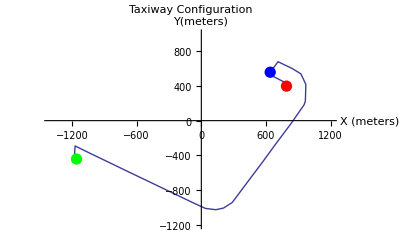

```mathematica
Show[{a,arrivalnode,spotnode,gatenode},PlotRange->{{-1400,1200},{-1200,1000}},PlotLabel->"Taxiway Configuration", AxesLabel->{"X (meters)", "Y(meters)"}]
```

```mathematica
L
```